```mathematica
Quit
```

### References

[1] Yang, Zhen-Hao and Wu, Liang-Bi and Kuang, Xiao-Mei and Qian, Wei-Liang, “QNM families: classification and competition”, e - Print : [arXiv:1004.4007]  https://arxiv.org/pdf/2510.02033.

[2] JBlazquez-Salcedo, Jose Luis and Macedo, Caio F. B. and Cardoso, Vitor and Ferrari, Valeria and Gualtieri, Leonardo and Khoo, Fech Scen and Kunz, Jutta and Pani, Paolo, “Perturbed black holes in Einstein-dilaton-Gauss-Bonnet gravity: Stability, ringdown, and gravitational-wave emission”, Phys. Rev. D 94, no.10, 104024 (2016), [arXiv:1609.01286] https://arxiv.org/pdf/1609.01286.

### Initial setting

```mathematica
SP=Simplify;
FS=FullSimplify;
VA=Variables;
SP9[nu_]:=SetPrecision[nu,9]
precs=8*MachinePrecision;
YOULI[TU_]:=Rationalize[Chop[Expand[N[TU,precs]],10^-precs],10^-precs];
```

### Metric, Master Equations, Potentials

```mathematica
({{-A1[r], 0, 0, 0}, {0, 1/B1[r], 0, 0}, {0, 0, C1[r], 0}, {0, 0, 0, C1[r] Sin[θ]^2}});
mlo==1/(M-lo/2);
tobh1={A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)],B1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)],C1->Function[r,r^2]};
```

```mathematica
(*V with any spins*)
Vgeneral=A1[r](λ/r^2+(1-s)A1'[r]/r+s-2 A1''[r]);
Vgeneral/.s->#&/@{2,1,0}
EOMasr0=(ω^2-𝒱[r]) ψ[r]+A1[r] A1'[r] ψ'[r]+A1[r]^2 ψ''[r]/.𝒱->Function[r,A1[r](λ/r^2+(1-s)A1'[r]/r+s2(*s-2*)A1''[r])]/.s2->s-2/.s->s/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]//SP
EOMasr0/.s->1//SP
```

{A1[r] (λ/r^2-A1'[r]/r+A1''[r]),(λ A1[r])/r^2,A1[r] (λ/r^2+A1'[r]/r)}

(ω^2-(ⅇ^(-2 mlo r) (ⅇ^(mlo r) (-2 M+r)+r α) (ⅇ^(mlo r) (l (1+l) r-2 M (-1+s))+mlo r^2 (-1+s) α+(-4 ⅇ^(mlo r) M+mlo^2 r^3 α) 2-s))/r^4) ψ[r]+(1-(2 M)/r+ⅇ^(-mlo r) α) ((2 M)/r^2-ⅇ^(-mlo r) mlo α) ψ'[r]+(1-(2 M)/r+ⅇ^(-mlo r) α)^2 ψ''[r]

(-(ⅇ^(-mlo r) l (1+l) (ⅇ^(mlo r) (-2 M+r)+r α))/r^3+ω^2) ψ[r]+(1-(2 M)/r+ⅇ^(-mlo r) α) ((2 M)/r^2-ⅇ^(-mlo r) mlo α) ψ'[r]+(1-(2 M)/r+ⅇ^(-mlo r) α)^2 ψ''[r]

### Setting boundary values

```mathematica
SetDirectory[NotebookDirectory[]];
seriesHa=<<"general_seriesHa_13";
asolall=<<"general_asolall_13";
seriesINFb=<<"general_seriesINFb_14";
bsolall=<<"general_bsolall_14";
```

-Graphics-

```mathematica
seriesHa[[4]]
```

hh[0] (Α_4[0]+Α_1[0] Α_4[1]+(Α_2[0]+Α_1[0] Α_2[1]) Α_4[2]+(Α_3[0]+Α_2[0] Α_3[2]+Α_1[0] (Α_3[1]+Α_2[1] Α_3[2])) Α_4[3])

```mathematica
asolall[[;;,-1]]//VA
seriesHa//VA
bsolall[[;;,-1]]//VA
seriesINFb//VA
```

{f1,rh,s,s2,λ,ω,A1'[rh],A1''[rh],A1^(3)[rh],A1^(4)[rh],A1^(5)[rh],A1^(6)[rh],A1^(7)[rh],A1^(8)[rh],A1^(9)[rh],A1^(10)[rh],A1^(11)[rh],A1^(12)[rh],A1^(13)[rh],A1^(14)[rh],A1^(15)[rh]}

{hh[0],Α_1[0],Α_2[0],Α_2[1],Α_3[0],Α_3[1],Α_3[2],Α_4[0],Α_4[1],Α_4[2],Α_4[3],Α_5[0],Α_5[1],Α_5[2],Α_5[3],Α_5[4],Α_6[0],Α_6[1],Α_6[2],Α_6[3],Α_6[4],Α_6[5],Α_7[0],Α_7[1],Α_7[2],Α_7[3],Α_7[4],Α_7[5],Α_7[6],Α_8[0],Α_8[1],Α_8[2],Α_8[3],Α_8[4],Α_8[5],Α_8[6],Α_8[7],Α_9[0],Α_9[1],Α_9[2],Α_9[3],Α_9[4],Α_9[5],Α_9[6],Α_9[7],Α_9[8],Α_10[0],Α_10[1],Α_10[2],Α_10[3],Α_10[4],Α_10[5],Α_10[6],Α_10[7],Α_10[8],Α_10[9],Α_11[0],Α_11[1],Α_11[2],Α_11[3],Α_11[4],Α_11[5],Α_11[6],Α_11[7],Α_11[8],Α_11[9],Α_11[10],Α_12[0],Α_12[1],Α_12[2],Α_12[3],Α_12[4],Α_12[5],Α_12[6],Α_12[7],Α_12[8],Α_12[9],Α_12[10],Α_12[11],Α_13[0],Α_13[1],Α_13[2],Α_13[3],Α_13[4],Α_13[5],Α_13[6],Α_13[7],Α_13[8],Α_13[9],Α_13[10],Α_13[11],Α_13[12],Α_14[0],Α_14[1],Α_14[2],Α_14[3],Α_14[4],Α_14[5],Α_14[6],Α_14[7],Α_14[8],Α_14[9],Α_14[10],Α_14[11],Α_14[12],Α_14[13]}

{s,s2,λ,ω,Ainf[0],Ainf[1],Ainf[2],Ainf[3],Ainf[4],Ainf[5],Ainf[6],Ainf[7],Ainf[8],Ainf[9],Ainf[10],Ainf[11],Ainf[12]}

{ginf[0],Β_1[0],Β_2[0],Β_2[1],Β_3[0],Β_3[1],Β_3[2],Β_4[0],Β_4[1],Β_4[2],Β_4[3],Β_5[0],Β_5[1],Β_5[2],Β_5[3],Β_5[4],Β_6[0],Β_6[1],Β_6[2],Β_6[3],Β_6[4],Β_6[5],Β_7[0],Β_7[1],Β_7[2],Β_7[3],Β_7[4],Β_7[5],Β_7[6],Β_8[0],Β_8[1],Β_8[2],Β_8[3],Β_8[4],Β_8[5],Β_8[6],Β_8[7],Β_9[0],Β_9[1],Β_9[2],Β_9[3],Β_9[4],Β_9[5],Β_9[6],Β_9[7],Β_9[8],Β_10[0],Β_10[1],Β_10[2],Β_10[3],Β_10[4],Β_10[5],Β_10[6],Β_10[7],Β_10[8],Β_10[9],Β_11[0],Β_11[1],Β_11[2],Β_11[3],Β_11[4],Β_11[5],Β_11[6],Β_11[7],Β_11[8],Β_11[9],Β_11[10],Β_12[0],Β_12[1],Β_12[2],Β_12[3],Β_12[4],Β_12[5],Β_12[6],Β_12[7],Β_12[8],Β_12[9],Β_12[10],Β_12[11],Β_13[0],Β_13[1],Β_13[2],Β_13[3],Β_13[4],Β_13[5],Β_13[6],Β_13[7],Β_13[8],Β_13[9],Β_13[10],Β_13[11],Β_13[12]}

-Graphics-

```mathematica
asolall[[1;;5]](*First 5 terms in Subscript[Λ, ji]=Subscript[Α, j][i]*)/.Α:>Λ/.{f1->κ,A1->f,λ->ℓ(ℓ+1),s2->Subscript[δ, s-2],rh->Subscript[r, h]}/. {f[rh]:>f,Derivative[n_][f][Subscript[r, h]]:>Derivative[n][Subscript[f, Subscript[r, h]]]}//FS
bsolall[[1;;5]](*First 5 terms in Subscript[Υ, ki]=Subscript[Β, k][i]*)/.Β:>Υ/.{f1->κ,A1->f,λ->ℓ(ℓ+1),s2->Subscript[δ, s-2],rh->Subscript[r, h]}/. {Ainf[n_]:>Derivative[n][Subscript[f, ∞]]}//FS
asolall[[-14]](*Truncation order j = 14*)/.Α:>Λ/.{f1->κ,A1->f,λ->ℓ(ℓ+1),s2->Subscript[δ, s-2],rh->Subscript[r, h]}/. {f[rh]:>f,Derivative[n_][f][Subscript[r, h]]:>Derivative[n][Subscript[f, Subscript[r, h]]]}//FS
bsolall[[-1]](*Truncation order k = 13*)/.Β:>Υ/.{f1->κ,A1->f,λ->ℓ(ℓ+1),s2->Subscript[δ, s-2],rh->Subscript[r, h]}/. {Ainf[n_]:>Derivative[n][Subscript[f, ∞]]}//FS
```

{Λ_1[0]→(2 ℓ (1+ℓ) κ^2 (f_r_h')^2+r_h (-6 κ^2 ω^2 f_r_h'+(-2 (-1+s) κ^2+6 ω^2) (f_r_h')^3)+r_h^2 (κ^2 ω^2+(ω (ⅈ κ+ω)+2 κ^2 δ_(-2+s)) (f_r_h')^2) f_r_h'')/(2 r_h^2 (κ^2 ω^2 f_r_h'+(κ-ⅈ ω)^2 (f_r_h')^3)),Λ_2[1]→(2 f_r_h' (ℓ (1+ℓ) κ^2 f_r_h'+r_h (-3 κ^2 ω^2+(-((2+s) κ^2)+6 ⅈ κ ω+3 ω^2) (f_r_h')^2))+r_h^2 (κ^2 ω^2+(-2 κ^2+3 ⅈ κ ω+ω^2+2 κ^2 δ_(-2+s)) (f_r_h')^2) f_r_h'')/(2 r_h^2 (κ^2 ω^2 f_r_h'+(2 κ-ⅈ ω)^2 (f_r_h')^3)),Λ_2[0]→(-36 κ^2 ω^2 r_h (f_r_h')^2+12 (-2 (-1+s) κ^2+3 ω^2) r_h (f_r_h')^4-3 κ^2 ω^2 r_h^3 (f_r_h'')^2+2 κ^2 ω^2 r_h^2 f_r_h' (9 f_r_h''+r_h f_r_h^(3))+2 (f_r_h')^3 (6 ℓ (1+ℓ) κ^2+3 r_h^2 (3 ⅈ κ ω+3 ω^2+κ^2 (2-2 s+6 δ_(-2+s))) f_r_h''+r_h^3 (ω (2 ⅈ κ+ω)+6 κ^2 δ_(-2+s)) f_r_h^(3)))/(12 r_h^3 (f_r_h')^2 (κ^2 ω^2+(2 κ-ⅈ ω)^2 (f_r_h')^2)),Λ_3[2]→(2 f_r_h' (ℓ (1+ℓ) κ^2 f_r_h'+r_h (-3 κ^2 ω^2+(-((11+s) κ^2)+12 ⅈ κ ω+3 ω^2) (f_r_h')^2))+r_h^2 (κ^2 ω^2+(-6 κ^2+5 ⅈ κ ω+ω^2+2 κ^2 δ_(-2+s)) (f_r_h')^2) f_r_h'')/(2 r_h^2 (κ^2 ω^2 f_r_h'+(3 κ-ⅈ ω)^2 (f_r_h')^3)),Λ_3[1]→(-36 κ^2 ω^2 r_h (f_r_h')^2-12 ((1+2 s) κ^2-6 ⅈ κ ω-3 ω^2) r_h (f_r_h')^4-3 κ^2 ω^2 r_h^3 (f_r_h'')^2+2 κ^2 ω^2 r_h^2 f_r_h' (9 f_r_h''+r_h f_r_h^(3))+2 (f_r_h')^3 (6 ℓ (1+ℓ) κ^2-3 r_h^2 (-9 ⅈ κ ω-3 ω^2+2 κ^2 (2+s-3 δ_(-2+s))) f_r_h''+r_h^3 (4 ⅈ κ ω+ω^2+κ^2 (-3+6 δ_(-2+s))) f_r_h^(3)))/(12 r_h^3 (f_r_h')^2 (κ^2 ω^2+(3 κ-ⅈ ω)^2 (f_r_h')^2))}

{Υ_1[0]→(ⅈ ℓ (1+ℓ))/(2 ω),Υ_2[0]→(ⅈ (ℓ (1+ℓ)+f_∞ (-1+s+2 δ_(-2+s))) f_∞')/(4 ω f_∞),Υ_2[1]→(ⅈ (ℓ+ℓ^2-2 f_∞))/(4 ω)-(f_∞')/(2 f_∞),Υ_3[0]→(ⅈ ((-1+s+2 δ_(-2+s)) (f_∞')^2+(ℓ (1+ℓ)+2 f_∞ (-1+s+3 δ_(-2+s))) f_∞''))/(6 ω f_∞),Υ_3[1]→(ⅈ (ℓ (1+ℓ)+f_∞ (-6+s+2 δ_(-2+s))) f_∞'-2 ω f_∞'')/(6 ω f_∞)}

Λ_14[13]→(2 f_r_h' (ℓ (1+ℓ) κ^2 f_r_h'+r_h (-3 κ^2 ω^2+(-((506+s) κ^2)+78 ⅈ κ ω+3 ω^2) (f_r_h')^2))+r_h^2 (κ^2 ω^2+(-182 κ^2+27 ⅈ κ ω+ω^2+2 κ^2 δ_(-2+s)) (f_r_h')^2) f_r_h'')/(2 r_h^2 (κ^2 ω^2 f_r_h'+(14 κ-ⅈ ω)^2 (f_r_h')^3))

Υ_13[12]→1/26 ((ⅈ (ℓ+ℓ^2-156 f_∞))/ω-(24 f_∞')/(f_∞))

-Graphics-

#### Construct integrator

```mathematica
Clear[getrh,DI0]
```

```mathematica
getrh[M0_,L0_,α0_,lo0_]:=Module[{mloVal,eqHor,rhGuess,rhVal},mloVal=1/(M0-(lo0*M0)/2);
acc=4*MachinePrecision;rsn=30;
eqHor=1-(2 M0)/r+α0 E^(-mloVal r);
rhGuess=FindInstance[eqHor==0,r,Reals][[1,-1]]//Values;
rhVal=FindRoot[eqHor,{r,rhGuess},WorkingPrecision->acc,PrecisionGoal->acc][[-1,-1]];
rhm=SetPrecision[rhVal,acc]//YOULI;
paras0={M->M0,lo->lo0*M0,rh->rhm,α->α0,l->L0,mlo->mloVal,hh[0]->1,ginf[0]->1}//SetPrecision[#,acc]&;
paras0]

(*This integrator is based on the MMA notebook outlined in Paolo Pani et al.,arXiv:1609.01286. *)
DI0[ωVal_,rMatch_,δh_,rInfInit_,h0_,g0_]:=Module[{solOpts,currentRules,rIn,rOut,bcIn,bcOut,solIn,solOut,ψIn,ψOut,ratio,diff},solOpts={MaxSteps->Infinity,PrecisionGoal->13,AccuracyGoal->13,Method->"StiffnessSwitching",InterpolationOrder->All};
currentRules=Join[paras0,{ω->ωVal,δh->δh,δinf->rInfInit,hh[0]->h0,ginf[0]->g0}]//YOULI;
EQs={EOMasr==0}//.currentRules;
rIn=rhm (1+δh)//.currentRules;rOut=rInfInit//.currentRules;bcIn={ψ[rIn]==bdeqh,ψ'[rIn]==bdeqhp}/. r->rIn//.currentRules;
bcOut={ψ[rOut]==bdeqi,ψ'[rOut]==bdeqip}/. r->rOut//.currentRules;
solIn=NDSolve[Union[EQs,bcIn],ψ,{r,rIn,rMatch},solOpts][[1]];
solOut=NDSolve[Union[EQs,bcOut],ψ,{r,rOut,rMatch},solOpts][[1]];
ψIn=ψ[r]/. solIn;
ψOut=ψ[r]/. solOut;
ratio=(ψIn/ψOut)/. r->rMatch;
ψn=PiecewiseData=Piecewise[{{ψIn,r<rMatch},{ratio*ψOut,r>=rMatch}}];
diff=(D[ψIn,r]-D[ratio*ψOut,r])/D[ψIn,r]/. r->rMatch;
{diff}]
```

### Start shooting

#### s=1, M=1, L=6, a=7.0, l0=0.952

```mathematica
getrh[1,6,700/100,952/1000]//YOULI
```

{M→1,lo→119/125,rh→57589304815235410440494146490221/78476289819753334553122260050476,α→7,l→6,mlo→250/131,hh[0]→1,ginf[0]→1}

```mathematica
f1s=(2 M)/rh^2-ⅇ^(-mlo rh) mlo α;ORDINF=14;ORDH=13;
(*field spin*)s0=1;Ainf[#]->SeriesCoefficient[1-(2*M)/r+α ⅇ^(-mlo r),{r,∞,#}]&/@Range[0,ORDINF+5];
GDA1=%//.paras0;
asolall2=asolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s//.paras0;
bsolall2=bsolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s/.GDA1//.paras0;
("Variables = "<>ToString[bsolall2[[;;,-1]]//VA])//PrintTemporary;
("Variables = "<>ToString[asolall2[[;;,-1]]//VA])//PrintTemporary;
PrintTemporary["Simplifying  Coefficients Α_1[0],Α_2[1]... ,Β_1[0],Β_2[0]..."];
Monitor[asolall3=Table[asolsp=SP[asolall2[[ii]],TimeConstraint->10],{ii,1,Length[asolall2]}],asolsp];
Monitor[bsolall3=Table[bsolsp=SP[bsolall2[[ii]],TimeConstraint->10],{ii,1,Length[bsolall2]}],bsolsp];
PrintTemporary["Substitute Coefficients Α_i[j],Β_i[j] into boundary series solutions seriesH & seriesINF "];
seriesHa1=seriesHa//.paras0/.asolall3//SetPrecision[#,3*MachinePrecision]&;
seriesINFb1=seriesINFb//.paras0/.bsolall3//SetPrecision[#,3*MachinePrecision]&;
PrintTemporary["Simplifying boundary series solutions seriesH & seriesINF"];
Monitor[seriesHs=Table[seriesHsp=SP[seriesHa1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;hh[ii]->seriesHsp,{ii,1,Length[seriesHa1]}],seriesHsp];
Monitor[seriesINFs=Table[seriesINFsp=SP[seriesINFb1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;ginf[ii]->seriesINFsp,{ii,1,Length[seriesINFb1]}],seriesINFsp];

temptext=PrintTemporary["computing bdeqh & bdeqi"];
bdeqh=(r-rh)^((-ⅈ ω 1)/f1)Sum[hh[i] (r-rhm)^i,{i,0,ORDH+1}]//.seriesHs/.{f1->f1s}/.(#&)/@paras0;
bdeqi=ⅇ^(ⅈ ω (rs))Sum[ginf[i]/r^i,{i,0,ORDINF-1}]//.seriesINFs/.{rs->rsn,f1->f1s}/.(#&)/@paras0;
temptext=PrintTemporary["computing bdeqhp & bdeqip"];
bdeqhp=D[bdeqh, r]/.(#&)/@paras0;
bdeqip=D[bdeqi, r]+(ⅈ ω)/A1[r](*∂_r ⅇ^(ⅈ ω (rsn))*)bdeqi/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.(#&)/@paras0;
(*bdeqhp//VA
bdeqip//VA*)
EOMasr=(ω^2-𝒱[r]) ψ[r]+A1[r] A1'[r] ψ'[r]+A1[r]^2 ψ''[r]/.𝒱->Function[r,A1[r](λ/r^2+(1-s)A1'[r]/r+s2(*s-2*)A1''[r])]/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]//SP;
```

```mathematica
(*QNM data from pseudospectral*)
EMqnml6m1a700lo952={1.12122814625020200945959719540685554954600352485387289880884586629874323795598`59.25650111487657-1.5692300523101421635539589264898935846110988909334301190741644157694325`59.25650111487657*^-7 ⅈ,1.1951116880794635213963387101728941275084193855774256436367624521882075999203`59.25650111487657-0.00001354974335637404363706061190742515780655653775616723099055503544260335792`59.25650111487657 ⅈ,1.2617753047228755385363291351690236910028169704861326035213305280714725607353`59.25650111487657-0.00043413572079851614105849420954273524826471109974936699208341262431265481273`59.25650111487657 ⅈ,1.31822830869983609685180993359541618031543100299872093745971706295471241257294`59.25650111487657-0.00487563333229363302371578561984377873545320775895491317457685179604376223853`59.25650111487657 ⅈ,1.36706443655465088226472770709088626214688530333660931574609159319503906096064`59.25650111487657-0.02047028436734878516449488325085388282531812825911324174621421473698829602254`59.25650111487657 ⅈ,1.41644627239350539882939296052022128954546646966156860954234730350951978302744`59.25650111487657-0.04840642428694233121232807668873131743017018817809544455380015582893006126197`59.25650111487657 ⅈ,1.4702975145754410542683390698000228728423358261406446040572962808936969666559`59.25650111487657-0.08335278407425851337492123932422328167709518810762405031260629504871745337961`59.25650111487657 ⅈ,1.52749008979487348390580929169703838189976616428398039466587854845446540340294`59.25650111487657-0.12218634273615176267825276598596889448129107595651633285633270990217279565309`59.25650111487657 ⅈ,1.58729721203157073549272810293684137718372607510408288688360791260419460866505`59.25650111487657-0.1640758841280431805383512366611323508470069033219811437909033575424844334893`59.25650111487657 ⅈ};
```

```mathematica
pseudo==EMqnml6m1a700lo952[[1]]
ωGuess=N[EMqnml6m1a700lo952[[1]],10];
targetFunc[ω_?NumericQ]:=DI0[ω,4*rhm,1*10^-4,90,1*10^-5,1*10^-1][[1]];
ωSol=Monitor[FindRoot[targetFunc[ω]==0,{ω,ωGuess},WorkingPrecision->15],ω]//Values//First;
shooting==ωSol
```

pseudo==1.1212281462502020094595971954068555495460035248538728988088-1.5692300523101421635539589264898935846110988909334301190742×10^-7 ⅈ

shooting==1.12122814625926-1.56930296618746×10^-7 ⅈ

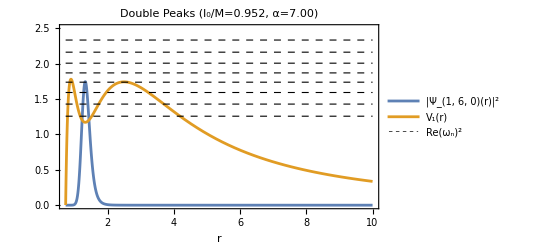

```mathematica
V5=Vgeneral/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.paras0//SP;
Plot[{1*10^-5.8 Abs[ψn]^2,V5//Evaluate,Re[EMqnml6m1a700lo952]^2},{r,rhm(1+10^-4),10},PlotRange->{{rhm,10},{0,2.5}},PlotStyle->{Null,Null,{Black,Dashed,Thickness[0.002]}},LabelStyle->Directive[FontFamily->"Times",FontSize->16],PlotLegends->{{"|Ψ_(1, 6, 0)(r)|^2","V_1(r)","Re(ω_n)^2"}},FrameTicksStyle->Directive[FontFamily->"Arial",FontSize->14],Frame->True,FrameLabel->{"r",None},PlotLabel->"Double Peaks (l_0/M=0.952, α=7.00)"]
```

#### s=1, M=1, L=6, a=7.0, l0=0.910

```mathematica
getrh[1,6,700/100,910/1000]//YOULI
```

{M→1,lo→91/100,rh→43146358461312335760225847927102/71403797591839205527537510923069,α→7,l→6,mlo→200/109,hh[0]→1,ginf[0]→1}

```mathematica
f1s=(2 M)/rh^2-ⅇ^(-mlo rh) mlo α;ORDINF=14;ORDH=13;
(*field spin*)s0=1;(*s2==Subscript[δ, s-2]*)nogw=0;gw2=1;Ainf[#]->SeriesCoefficient[1-(2*M)/r+α ⅇ^(-mlo r),{r,∞,#}]&/@Range[0,ORDINF+5];
GDA1=%//.paras0;
asolall2=asolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s//.paras0;
bsolall2=bsolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s/.GDA1//.paras0;
("Variables = "<>ToString[bsolall2[[;;,-1]]//VA])//PrintTemporary;
("Variables = "<>ToString[asolall2[[;;,-1]]//VA])//PrintTemporary;
PrintTemporary["Simplifying  Coefficients Α_1[0],Α_2[1]... ,Β_1[0],Β_2[0]..."];
Monitor[asolall3=Table[asolsp=SP[asolall2[[ii]],TimeConstraint->10],{ii,1,Length[asolall2]}],asolsp];
Monitor[bsolall3=Table[bsolsp=SP[bsolall2[[ii]],TimeConstraint->10],{ii,1,Length[bsolall2]}],bsolsp];
PrintTemporary["Substitute Coefficients Α_i[j],Β_i[j] into boundary series solutions seriesH & seriesINF "];
seriesHa1=seriesHa//.paras0/.asolall3//SetPrecision[#,3*MachinePrecision]&;
seriesINFb1=seriesINFb//.paras0/.bsolall3//SetPrecision[#,3*MachinePrecision]&;
PrintTemporary["Simplifying boundary series solutions seriesH & seriesINF"];
Monitor[seriesHs=Table[seriesHsp=SP[seriesHa1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;hh[ii]->seriesHsp,{ii,1,Length[seriesHa1]}],seriesHsp];
Monitor[seriesINFs=Table[seriesINFsp=SP[seriesINFb1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;ginf[ii]->seriesINFsp,{ii,1,Length[seriesINFb1]}],seriesINFsp];

temptext=PrintTemporary["computing bdeqh & bdeqi"];
bdeqh=(r-rh)^((-ⅈ ω 1)/f1)Sum[hh[i] (r-rhm)^i,{i,0,ORDH+1}]//.seriesHs/.{f1->f1s}/.(#&)/@paras0;
bdeqi=ⅇ^(ⅈ ω (rs))Sum[ginf[i]/r^i,{i,0,ORDINF-1}]//.seriesINFs/.{rs->rsn,f1->f1s}/.(#&)/@paras0;
temptext=PrintTemporary["computing bdeqhp & bdeqip"];
bdeqhp=D[bdeqh, r]/.(#&)/@paras0;
bdeqip=D[bdeqi, r]+(ⅈ ω)/A1[r](*∂_r ⅇ^(ⅈ ω (rsn))*)bdeqi/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.(#&)/@paras0;
(*bdeqhp//VA
bdeqip//VA*)
EOMasr=(ω^2-𝒱[r]) ψ[r]+A1[r] A1'[r] ψ'[r]+A1[r]^2 ψ''[r]/.𝒱->Function[r,A1[r](λ/r^2+(1-s)A1'[r]/r+s2(*s-2*)A1''[r])]/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]//SP;
```

```mathematica
(*QNM data from pseudospectral*)
EMqnml6m1a700lo910={1.40571108402509349478913881150039212421049026123955329323945100937717351852668`59.452916329910536-0.03330158327139827665039372857966674369418442469091683343750361986509721267905`59.452916329910536 ⅈ,1.50098289107105447770012898818421282813244379574808822986361264069727363813177`59.452916329910536-0.10072312371919206755720186813379898271750206162447055248945811677386428914035`59.452916329910536 ⅈ,1.61221414724271980755831554245336338084248584931572292189978569805629276182885`59.452916329910536-0.17409385178446622753144511433918056005035782341420534638896579291312031916507`59.452916329910536 ⅈ,2.73708946982061762567487241742097867678265563334009702513131948951011332442313`59.452916329910536-0.21623164757587115507365013884777213661980876842570468310114036361577160759035`59.452916329910536 ⅈ};
```

```mathematica
pseudo==EMqnml6m1a700lo910[[1]]
ωGuess=N[EMqnml6m1a700lo910[[1]],10];
targetFunc[ω_?NumericQ]:=DI0[ω,4*rhm,1*10^-4,50,1*10^-5,1*10^-1][[1]];
ωSol=Monitor[FindRoot[targetFunc[ω]==0,{ω,ωGuess},WorkingPrecision->15],ω]//Values//First;
shooting==ωSol
```

pseudo==1.4057110840250934947891388115003921242104902612395532932395-0.033301583271398276650393728579666743694184424690916833437504 ⅈ

shooting==1.40692264745323-0.0325416581237505 ⅈ

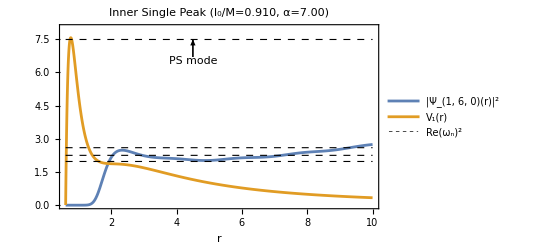

```mathematica
V5=Vgeneral/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.paras0//SP;
Plot[{1*10^-12.2 Abs[ψn]^2,V5//Evaluate,Re[EMqnml6m1a700lo910]^2},{r,rhm(1+10^-4),10},PlotRange->{{rhm,10},{0,8}},PlotStyle->{Null,Null,{Black,Dashed,Thickness[0.002]}},LabelStyle->Directive[FontFamily->"Times",FontSize->16],PlotLegends->{{"|Ψ_(1, 6, 0)(r)|^2","V_1(r)","Re(ω_n)^2"}},FrameTicksStyle->Directive[FontFamily->"Arial",FontSize->14],Frame->True,FrameLabel->{"r",None},PlotLabel->"Inner Single Peak (l_0/M=0.910, α=7.00)",Epilog->{
{Directive[Black,Thickness[0.003]],{Arrow[{{4.5,6.7},{4.5,7.5}}],Text[Style["PS mode",FontFamily->"Times",FontSize->11],{4.5,6.5}]}}}]
```

#### s=1, M=1, L=6, a=0.5, l0=0.910

```mathematica
getrh[1,6,50/100,910/1000]//YOULI
```

{M→1,lo→91/100,rh→344311969563788633634387027827358/174458403721139628720508665601117,α→1/2,l→6,mlo→200/109,hh[0]→1,ginf[0]→1}

```mathematica
f1s=(2 M)/rh^2-ⅇ^(-mlo rh) mlo α;ORDINF=14;ORDH=13;
(*field spin*)s0=1;(*s2==Subscript[δ, s-2]*)nogw=0;gw2=1;Ainf[#]->SeriesCoefficient[1-(2*M)/r+α ⅇ^(-mlo r),{r,∞,#}]&/@Range[0,ORDINF+5];
GDA1=%//.paras0;
asolall2=asolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s//.paras0;
bsolall2=bsolall/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.f1->f1s/.GDA1//.paras0;
("Variables = "<>ToString[bsolall2[[;;,-1]]//VA])//PrintTemporary;
("Variables = "<>ToString[asolall2[[;;,-1]]//VA])//PrintTemporary;
PrintTemporary["Simplifying  Coefficients Α_1[0],Α_2[1]... ,Β_1[0],Β_2[0]..."];
Monitor[asolall3=Table[asolsp=SP[asolall2[[ii]],TimeConstraint->10],{ii,1,Length[asolall2]}],asolsp];
Monitor[bsolall3=Table[bsolsp=SP[bsolall2[[ii]],TimeConstraint->10],{ii,1,Length[bsolall2]}],bsolsp];
PrintTemporary["Substitute Coefficients Α_i[j],Β_i[j] into boundary series solutions seriesH & seriesINF "];
seriesHa1=seriesHa//.paras0/.asolall3//SetPrecision[#,3*MachinePrecision]&;
seriesINFb1=seriesINFb//.paras0/.bsolall3//SetPrecision[#,3*MachinePrecision]&;
PrintTemporary["Simplifying boundary series solutions seriesH & seriesINF"];
Monitor[seriesHs=Table[seriesHsp=SP[seriesHa1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;hh[ii]->seriesHsp,{ii,1,Length[seriesHa1]}],seriesHsp];
Monitor[seriesINFs=Table[seriesINFsp=SP[seriesINFb1[[ii]],TimeConstraint->10]//SetPrecision[#,acc]&;ginf[ii]->seriesINFsp,{ii,1,Length[seriesINFb1]}],seriesINFsp];

temptext=PrintTemporary["computing bdeqh & bdeqi"];
bdeqh=(r-rh)^((-ⅈ ω 1)/f1)Sum[hh[i] (r-rhm)^i,{i,0,ORDH+1}]//.seriesHs/.{f1->f1s}/.(#&)/@paras0;
bdeqi=ⅇ^(ⅈ ω (rs))Sum[ginf[i]/r^i,{i,0,ORDINF-1}]//.seriesINFs/.{rs->rsn,f1->f1s}/.(#&)/@paras0;
temptext=PrintTemporary["computing bdeqhp & bdeqip"];
bdeqhp=D[bdeqh, r]/.(#&)/@paras0;
bdeqip=D[bdeqi, r]+(ⅈ ω)/A1[r] bdeqi/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.(#&)/@paras0;
(*bdeqhp//VA
bdeqip//VA*)
EOMasr=(ω^2-𝒱[r]) ψ[r]+A1[r] A1'[r] ψ'[r]+A1[r]^2 ψ''[r]/.𝒱->Function[r,A1[r](λ/r^2+(1-s)A1'[r]/r+s2(*s-2*)A1''[r])]/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]//SP;
```

```mathematica
(*QNM data from pseudospectral*)
EMqnml6m1a50lo910={1.24608213741913753573177137427734027297411299447176573504198058954461202114501`59.80834514420704-0.09493185723530523061779211466254098759973707167407772691957036565064881530926`59.80834514420704 ⅈ,1.23840995146462576534981392262815858006615846611551323694804445128385197010543`59.80834514420704-0.28564973203330344359426968861385282708329793923723264902765975783332972379372`59.80834514420704 ⅈ};
```

```mathematica
pseudo==EMqnml6m1a50lo910[[1]]
ωGuess=N[EMqnml6m1a50lo910[[1]],10];
targetFunc[ω_?NumericQ]:=DI0[ω,4*rhm,1*10^-4,19,1*10^-5,1*10^-1][[1]];
ωSol=Monitor[FindRoot[targetFunc[ω]==0,{ω,ωGuess},WorkingPrecision->14],ω]//Values//First;
shooting==%
```

pseudo==1.246082137419137535731771374277340272974112994471765735042-0.09493185723530523061779211466254098759973707167407772691957 ⅈ

shooting==1.2397864076597-0.095170659934576 ⅈ

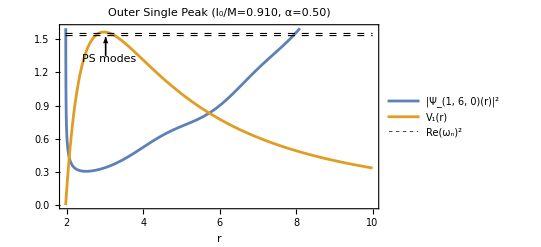

```mathematica
V5=Vgeneral/.s2->s-2/.s->s0/.λ->l(l+1)/.A1->Function[r,1-(2*M)/r+α ⅇ^(-mlo r)]/.paras0//SP;
Plot[{1*10^-0.8 Abs[ψn]^2,V5//Evaluate,Re[EMqnml6m1a50lo910]^2},{r,rhm(1+10^-4),10},PlotRange->{{rhm,10},{0,1.6}},PlotStyle->{Null,Null,{Black,Dashed,Thickness[0.002]}},LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameTicksStyle->Directive[FontFamily->"Arial",FontSize->14],
PlotLegends->{{"|Ψ_(1, 6, 0)(r)|^2","V_1(r)","Re(ω_n)^2"}},Frame->True,FrameLabel->{"r",None},PlotLabel->"Outer Single Peak (l_0/M=0.910, α=0.50)",Epilog->{
{Directive[Black,Thickness[0.003]],{Arrow[{{3.02,1.35},{3.02,1.52}}],Text[Style["PS modes",FontFamily->"Times",FontSize->11],{3.1,1.32}]}}}]
```